```mathematica
FileNameForTuple[primes_] := Module[{fileName, temp, sep, p, pPos},
sep = "\\";
temp ="d:\\triangle\DataSrc";
For[pPos =1, pPos <= Length[primes], pPos++,
temp = StringJoin[temp, sep, ToString[primes[[pPos]]]];
];
temp = StringJoin[temp, "\\Solutions.txt"];
fileName = temp;
Return[fileName]
]
```

```mathematica
Distance[n_,p_] := Module[ {threshold, digits, position, found, nextPower, result},
If [n ==0, Return[0]];
(* Initialize some precomputed local varables *)
threshold = (p-1)/2;
digits = IntegerDigits[n,p];

(* find the first digit above the threshold *)
found = -1;
For[ position = 1, position <=Length[digits], position++,
If [ digits [[position]] > threshold,
found = position; Break[]
]
];

(* if we didn't find a digit, then the distance is zero *)
If [found ==-1, Return[0]];

(* we did find a faulty digit.  Now we need to look before it for digits that equal the threshold.
If we would not count these then we would end up with a new value which is still not p-good (due
to the carrying) *)
While[ found >1,
If [ digits [[found-1]] == threshold,found --,Break[]]
];

(* if we have gone all the way to the start*)
If[found ==1,
Block[{},
nextPower= p^(Length[digits]);
Return[nextPower-n]
]
];


nextPower= p^(Length[digits]+1-found);
Return[nextPower-FromDigits[Take[digits,-(Length[digits]+1-found)],p]]
]
```

```mathematica
FileNameForVotes[primes_] := Module[{fileName, temp, sep, p, pPos},
sep = "\\";
temp ="d:\\triangle\Votes";
For[pPos =1, pPos <= Length[primes], pPos++,
temp = StringJoin[temp, sep, ToString[primes[[pPos]]]];
];
If [Not[DirectoryQ[temp]],
PrintTemporary["Creating directory " <> temp];
CreateDirectory[temp];

];
temp = StringJoin[temp, "\\Votes.txt"];
fileName = temp;
Return[fileName]
]
```

```mathematica
GoodForTuple[primes_] := Module[{fileName},
PrintTemporary[primes];
fileName = FileNameForTuple[primes];
If[Not[FileExistsQ[fileName]], Return[{}]
];
Return [ ReadList[fileName,Number] ]
]
```

```mathematica
VotesForTuple[primes_] := Module[{fileName},
PrintTemporary[primes];
fileName = FileNameForVotes[primes];
Print[fileName];
If[Not[FileExistsQ[fileName]], Return[{}]
];
Return [Map[#[[1]]&,Flatten[ReadList[fileName],1] ]]
]
```

```mathematica
VoteVectorsForTuple[primes_, stopAt_] := Module[{fileName, result},
fileName = FileNameForVotes[primes];
If[Not[FileExistsQ[fileName]], Return[{}]
];
PrintTemporary["Reading :" <> fileName <> " ..."];
result=ReadList[fileName,Expression,  stopAt] ;
PrintTemporary["Done."];
Return [result];
]
```

```mathematica
GraphForNumber2[n_,p_] := Module[
{result, pos, digs,f,t, lbl},
digs=IntegerDigits[n,p];
pos=1;
result={};
t= ToString[FromDigits[Take[digs,{1,pos}],p]] <> "-" <> ToString[Length[digs]-pos];
If [ Length[digs]==1, t=n];
 lbl=ToString[digs[[1]] ];
result={{"Start" -> t  ,lbl}};
For[pos=1, pos < Length[digs] , pos++,
f= ToString[FromDigits[Take[digs,{1,pos}],p]] <> "-" <> ToString[Length[digs]-pos];
t= ToString[FromDigits[Take[digs,{1,pos+1}],p]] <> "-" <> ToString[Length[digs]-pos-1];
If [pos == Length[digs]-1, t=n];
lbl=ToString[digs[[pos+1]] ];
result=Append[result, {f->t ,lbl}]
];
Return[result];
]
```

```mathematica
InternalCalculateVotes[primes_, count_] := Module[{ current,  maxdist, distanceTable, pos, fileName, previous},
fileName = FileNameForVotes[primes];
previous = VoteVectorsForTuple[primes,count];
If [Length[previous]==0,

pos =1;
current = 0;
,
pos = Length[previous];
current = previous[[pos]] [[1]] + Max[previous[[pos]][[2]]];
];

While[pos< count,
(*Print[current];*)
distanceTable = ParallelTable[Distance[current, p], {p, primes}];
With [
 {file = OpenAppend[fileName, PageWidth->20000]},
Write[file, {current,distanceTable}];
Close[file];
];
pos++;
If [Mod[pos,10000]==0,PrintTemporary[ToString[pos] <> " / " <> ToString[count]] <> " - " <> ToString[N[Log[10,current]]]];
maxdist = Max[distanceTable];
If[maxdist==0,
current +=1;
,
current += maxdist;
];
];
Return[VoteVectorsForTuple[primes,count]];
]
```

```mathematica
DynamicVoteList[primes_, count_] := InternalCalculateVotes[primes,count]
```

```mathematica
DynamicVoteList[primes_,start_, count_] := 
Take[DynamicVoteList[count+ start],{start,count}]
```

```mathematica
DrawTupleVotes[tuple_, range_] := Module[
{result},
result = With[{g=Map[#[[1]]&,DynamicVoteList[tuple, range[[2]]] ] },
Print[g];
Table[
With[
{threshold=(p+1)/2,
 start = Max[1,range[[1]]],
end= Min[Length[g],range[[2]]]},
TreePlot[
Flatten[Table[GraphForNumber2[i,p],{i, Take[g, {start, end}]}],1],
Left,
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->True,
EdgeRenderingFunction->Function[{pos,edge,lbl},
{If [FromDigits[lbl] < threshold,Blue, Red], Line[pos],Style[Inset[lbl,Mean[pos],Automatic,Automatic,Background->White],FontFamily->"Calibri", FontSize->Larger]}
],
VertexRenderingFunction->Function[{pos,vertex},If[NumericQ[vertex],
{Background->If[Max[Table[Distance[vertex,pl],{pl, tuple}]]==0, Green,
If[Distance[vertex,p]==0, Orange, Red]
],EdgeForm[Black],Black,Style[Text[vertex,pos],FontFamily->"Calibri", FontSize->Tiny, FontColor->White]}
,
{PointSize[0.001],Point[pos]}
]
],
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfor vote "  <> ToString[start ]<> " to " <> ToString[ end],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
]
],
{p,tuple}
]
];
Return[result]
]
```

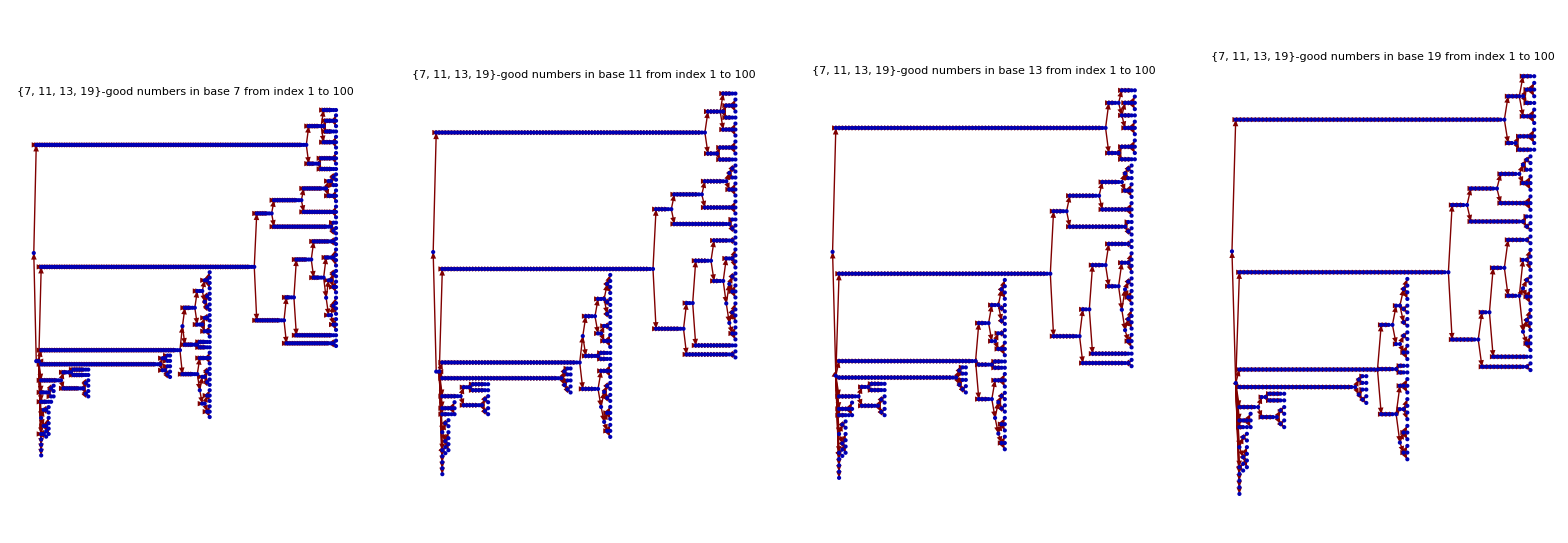

```mathematica
With[{tuple={7,11,13,19}, range={1,100}},
With[{g=GoodForTuple[tuple]},
GraphicsRow[
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,Take[g, {Max[1, range[[1]]], Min[Length[g], range[[2]]]}]}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
]
```

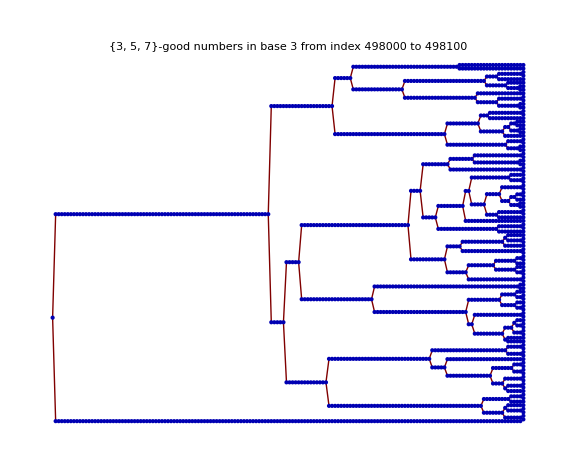
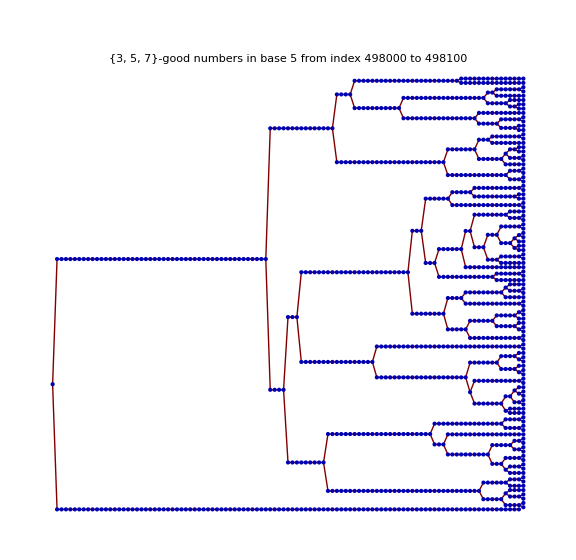
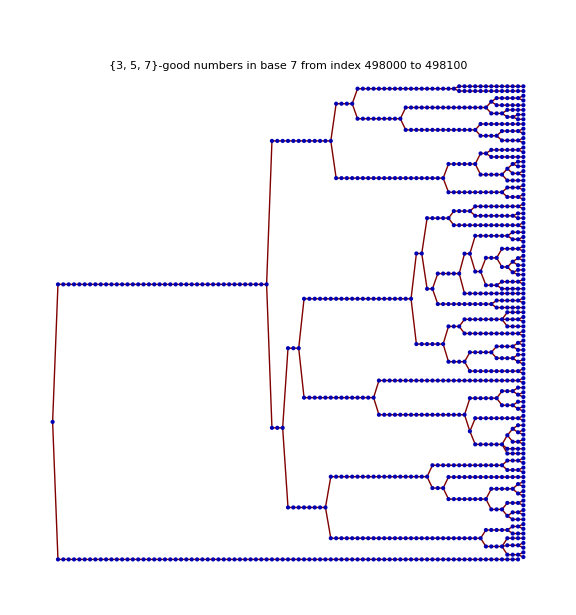

```mathematica
With[{tuple={3,5,7}, range={498000,498100}},
With[{g=GoodForTuple[tuple]},
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,Take[g, {Max[1, range[[1]]], Min[Length[g], range[[2]]]}]}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
```

140

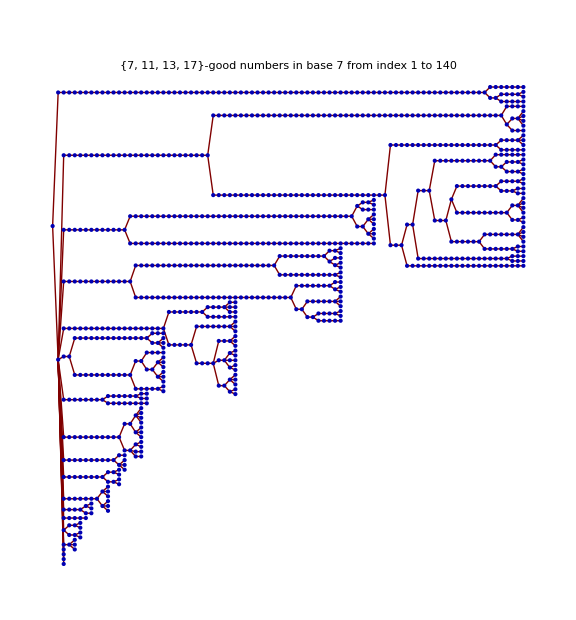
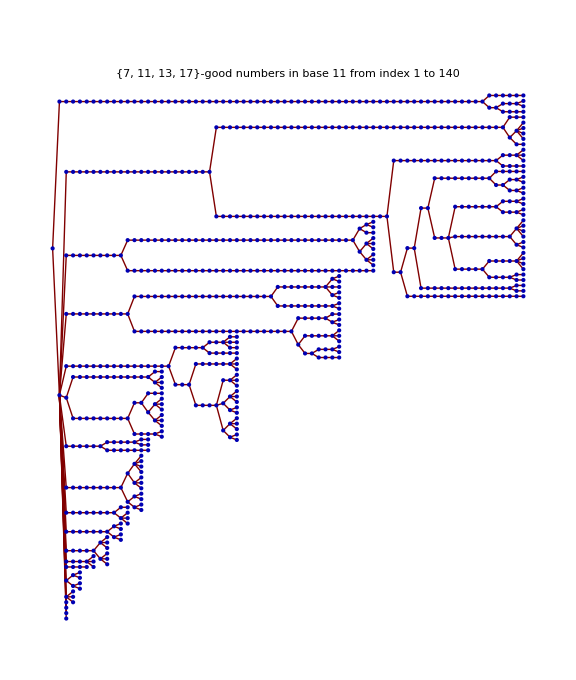
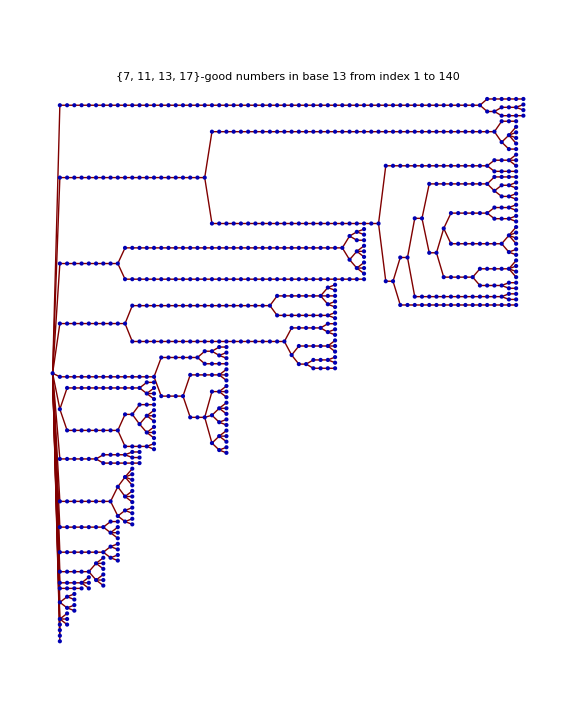
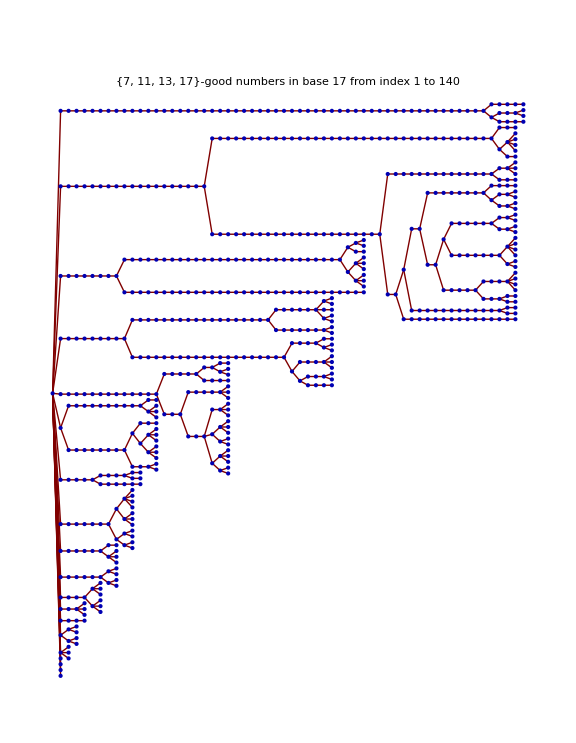

```mathematica
With[{tuple={7,11,13,17}, range={1,140}},
With[{g=GoodForTuple[tuple]},
Print[Length[g]];
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,Take[g, {Max[1, range[[1]]], Min[Length[g], range[[2]]] }]}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
```

8

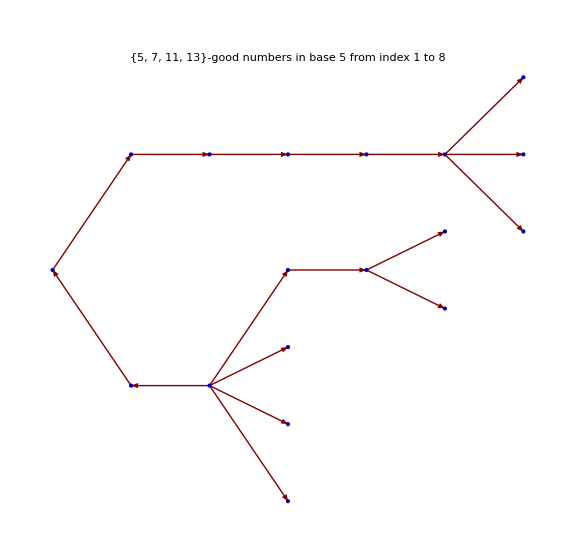
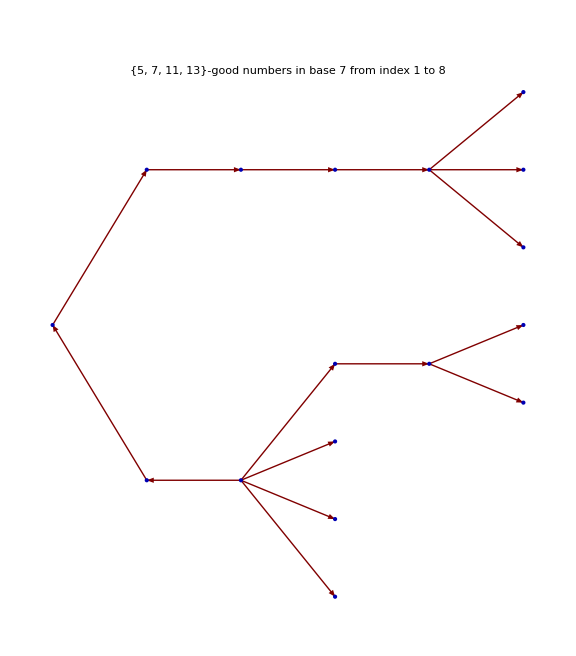
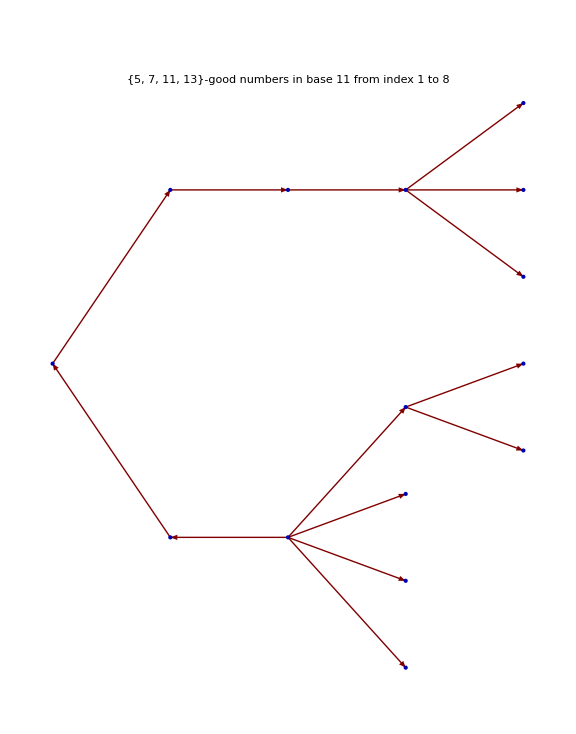
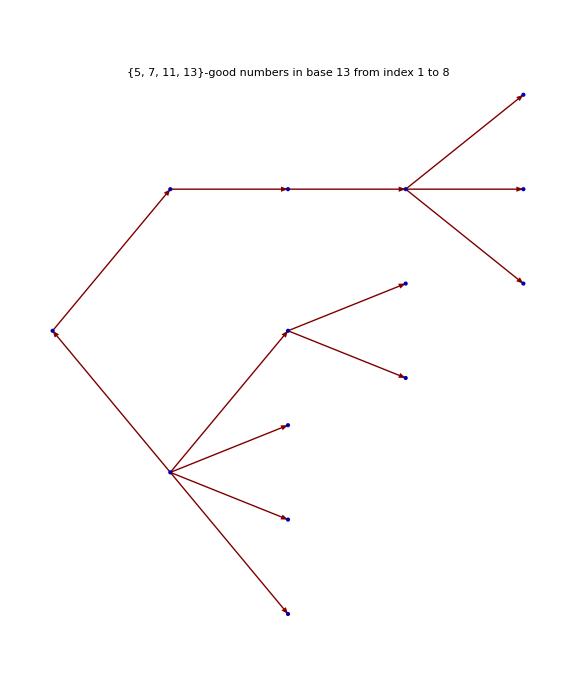

```mathematica
With[{tuple={5,7,11,13}, range={1,100}},
With[{g=GoodForTuple[tuple]},
Print[Length[g]];
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,g}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->True,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
```

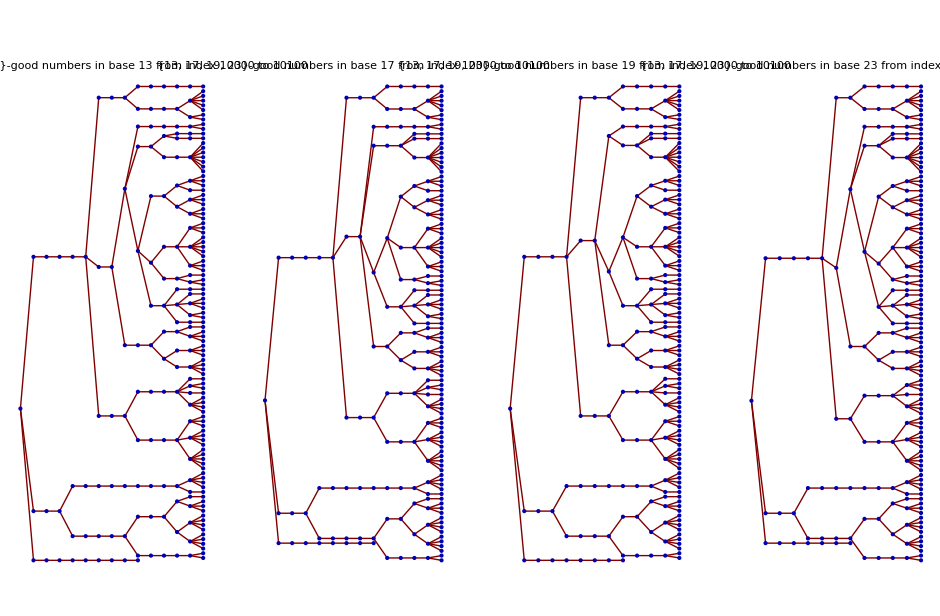

```mathematica
With[{tuple={13,17,19,23}, range={10000,10100}},
With[{g=GoodForTuple[tuple]},
GraphicsRow[
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,Take[g, {Max[1, range[[1]]], Min[Length[g], range[[2]]]}]}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
]
```

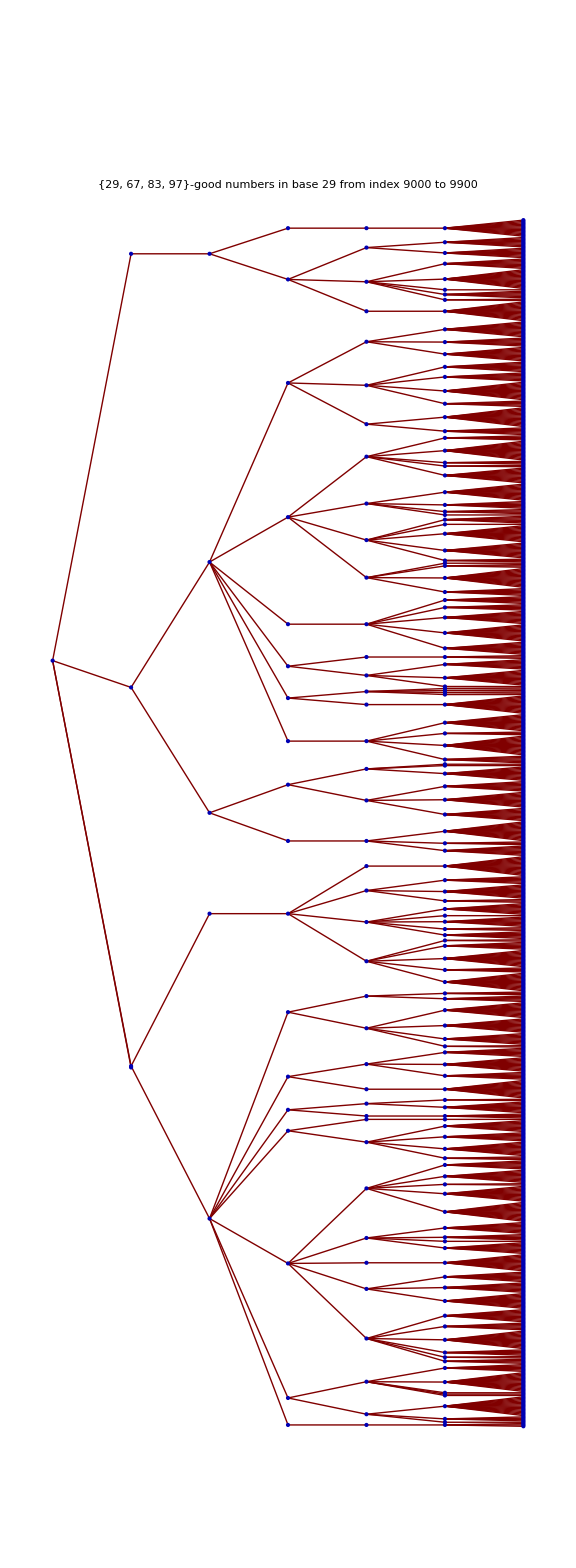
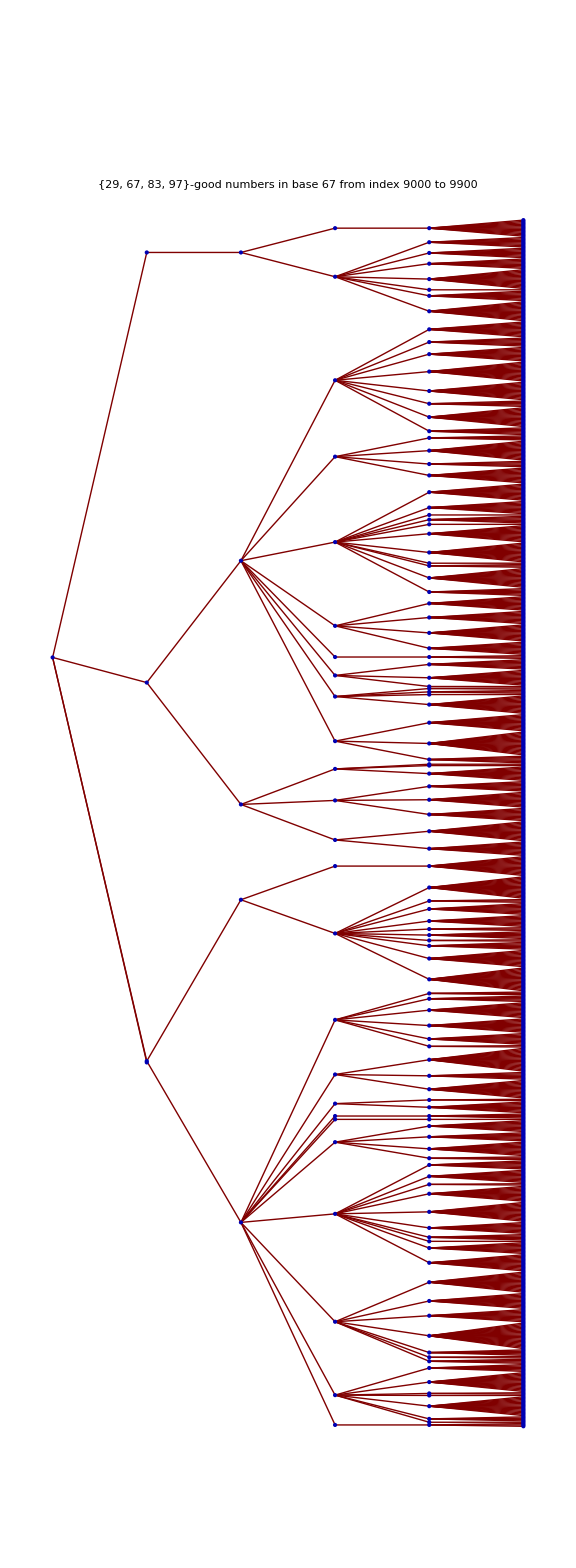
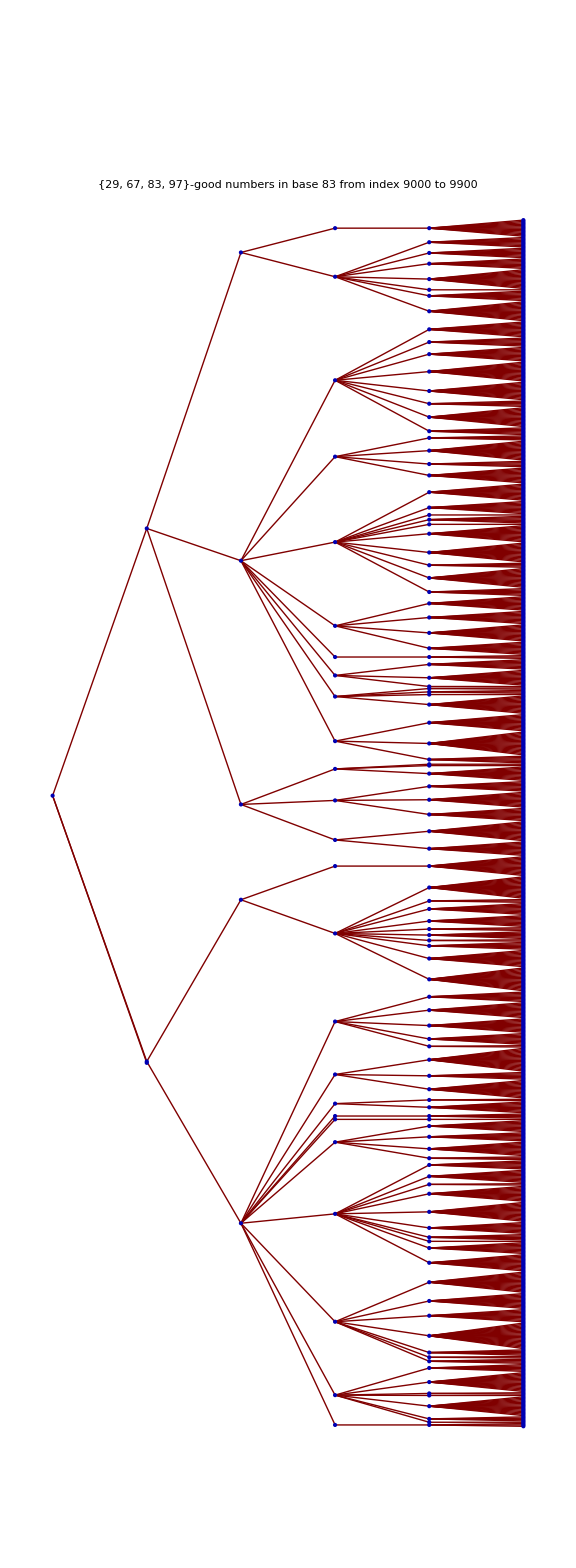
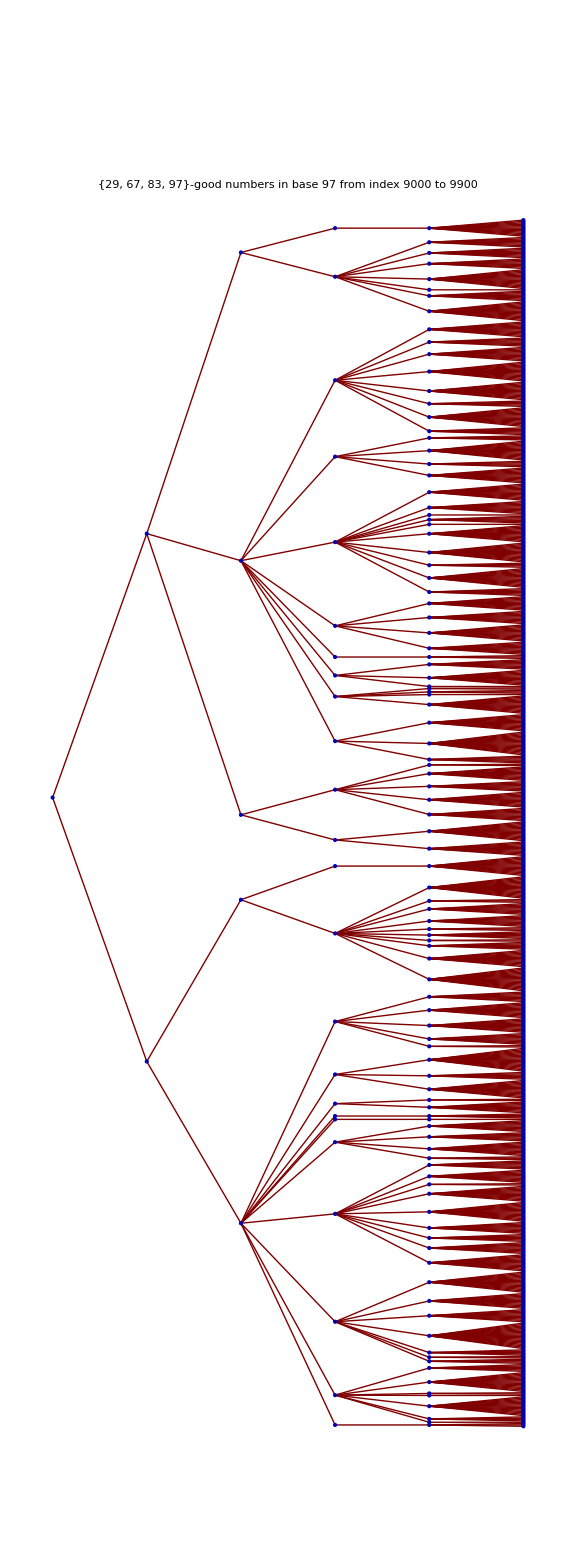

```mathematica
With[{tuple={29, 67,83,97}, range={9000,9900}},
With[{g=GoodForTuple[tuple]},
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,Take[g, {Max[1, range[[1]]], Min[Length[g], range[[2]]]}]}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
```

```mathematica
Length[GoodForTuple[{29, 67,83,97}]]
```

10277

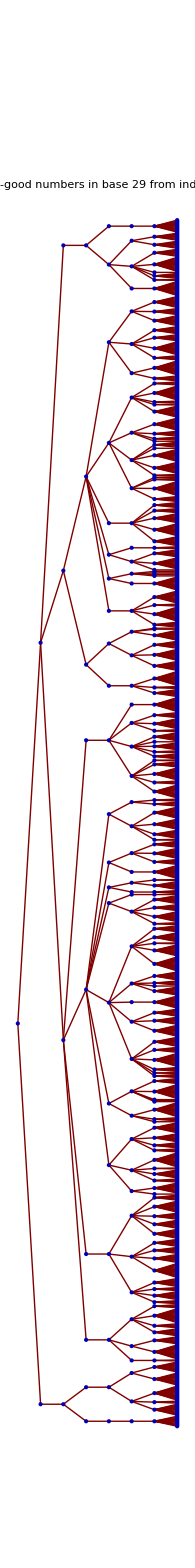
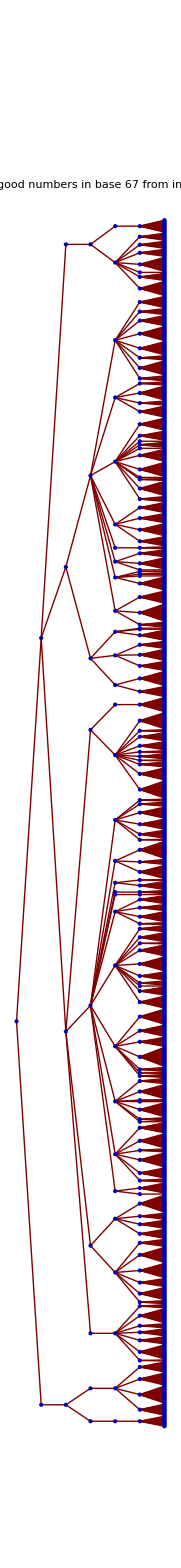
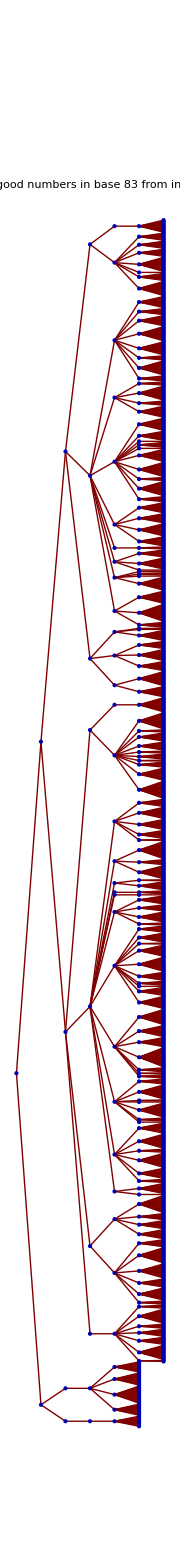
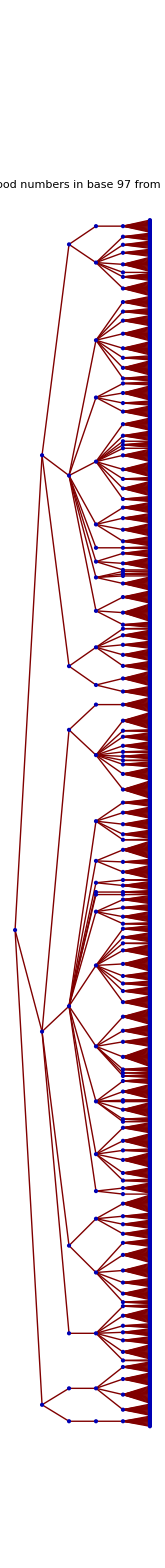

```mathematica
With[{tuple={29, 67,83,97}, range={8700,9900}},
With[{g=GoodForTuple[tuple]},
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,Take[g, {Max[1, range[[1]]], Min[Length[g], range[[2]]]}]}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
```

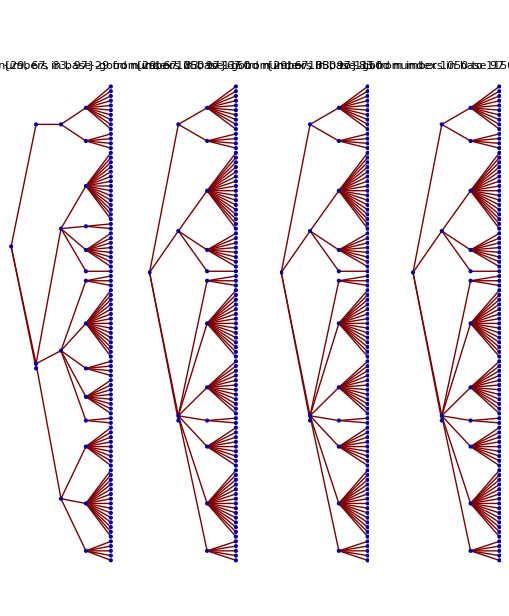

```mathematica
With[{tuple={29, 67,83,97}, range={1050,1150}},
With[{g=GoodForTuple[tuple]},
GraphicsRow[
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,Take[g, {Max[1, range[[1]]], Min[Length[g], range[[2]]]}]}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
]
```

9281

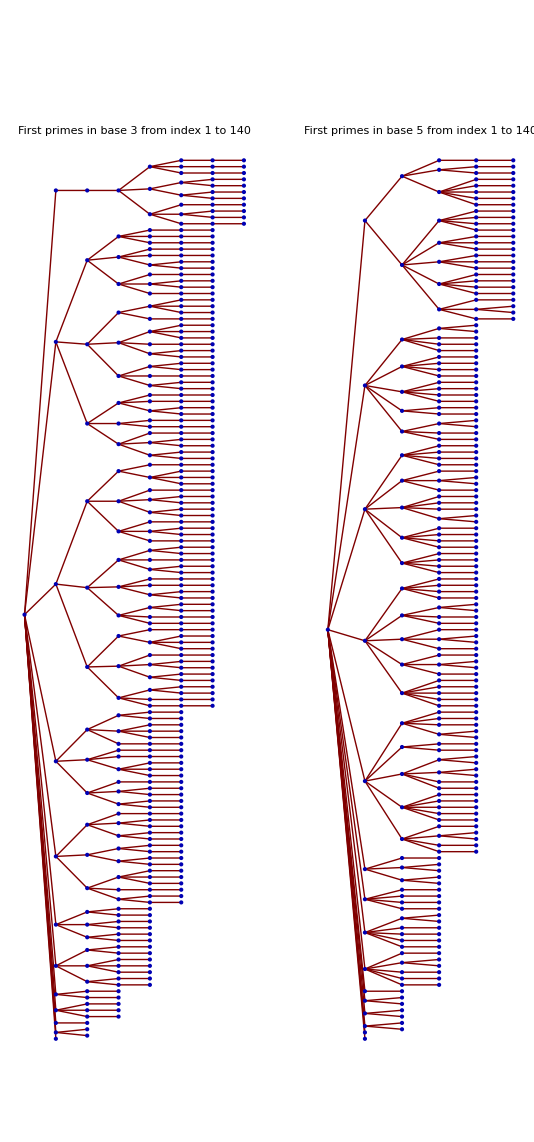

```mathematica
With[{tuple={3,5}, range={1,140}},
With[{g=GoodForTuple[tuple]},
Print[Length[g]];
GraphicsRow[
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,Prime[Range[1,140]]}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel->"First primes\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
]
```

9281

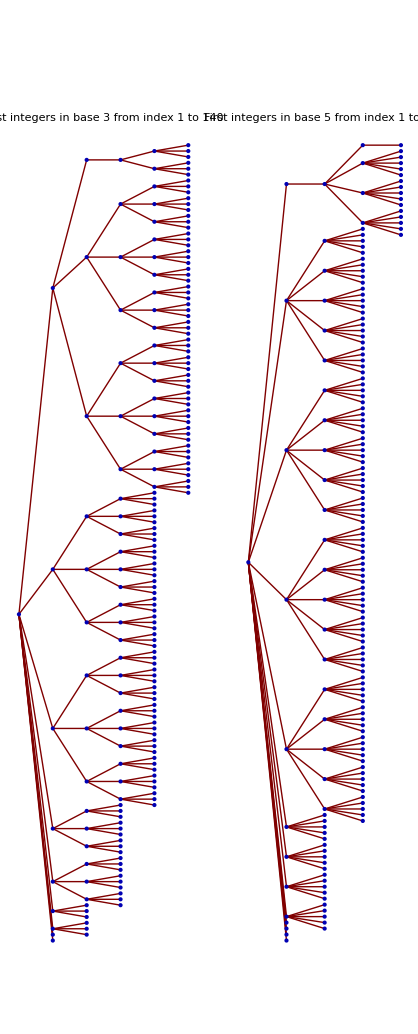

```mathematica
With[{tuple={3,5}, range={1,140}},
With[{g=GoodForTuple[tuple]},
Print[Length[g]];
GraphicsRow[
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,1,140}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel->"First integers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
]
```

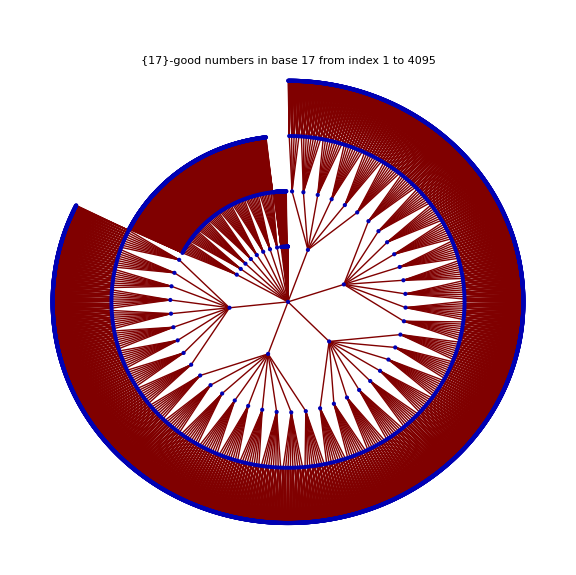

```mathematica
With[{tuple={17}, range={1,16^3-1}},
With[{g=GoodForTuple[tuple]},
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,Take[g, {Max[1, range[[1]]], Min[Length[g], range[[2]]]}]}],1],
Center, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->(range[[2]]-range[[1]])<100,
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
```

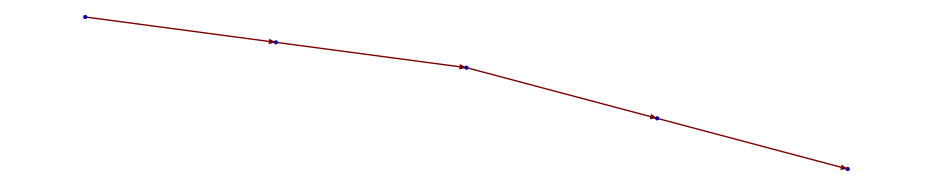

```mathematica
GraphPlot[
GraphForNumber2[1234,10],
MultiedgeStyle->None,
DirectedEdges->True,
VertexLabeling->False,
EdgeLabeling->True,
ImageSize->Large,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
]
```

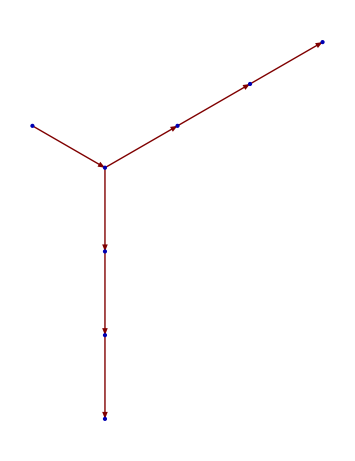

```mathematica
GraphPlot[
Join[GraphForNumber2[1234,10],GraphForNumber2[1111,10]],
MultiedgeStyle->None,
DirectedEdges->True,
VertexLabeling->False,
EdgeLabeling->True,
ImageSize->Large,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
Method->"RadialDrawing"
]
```

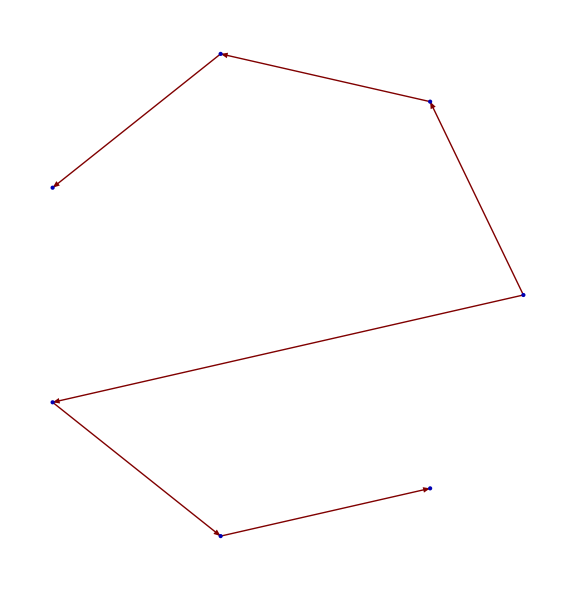

```mathematica
GraphPlot[
Join[GraphForNumber2[1234,11],GraphForNumber2[1111,11]],
MultiedgeStyle->None,
DirectedEdges->True,
VertexLabeling->False,
EdgeLabeling->True,
ImageSize->Large,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
Method->"CircularEmbedding"
]
```

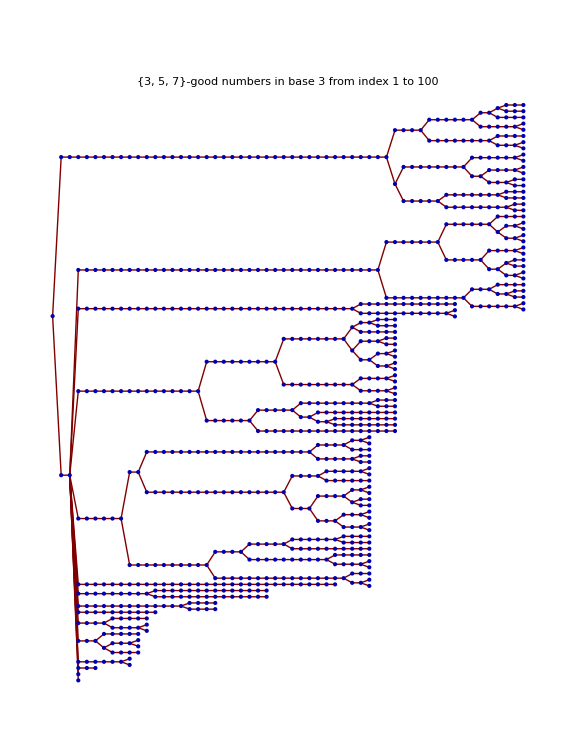
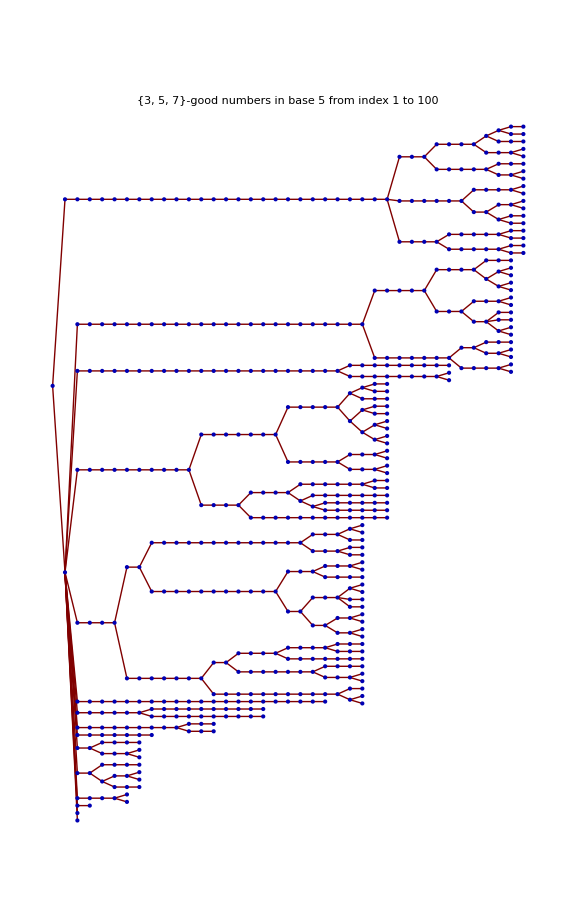
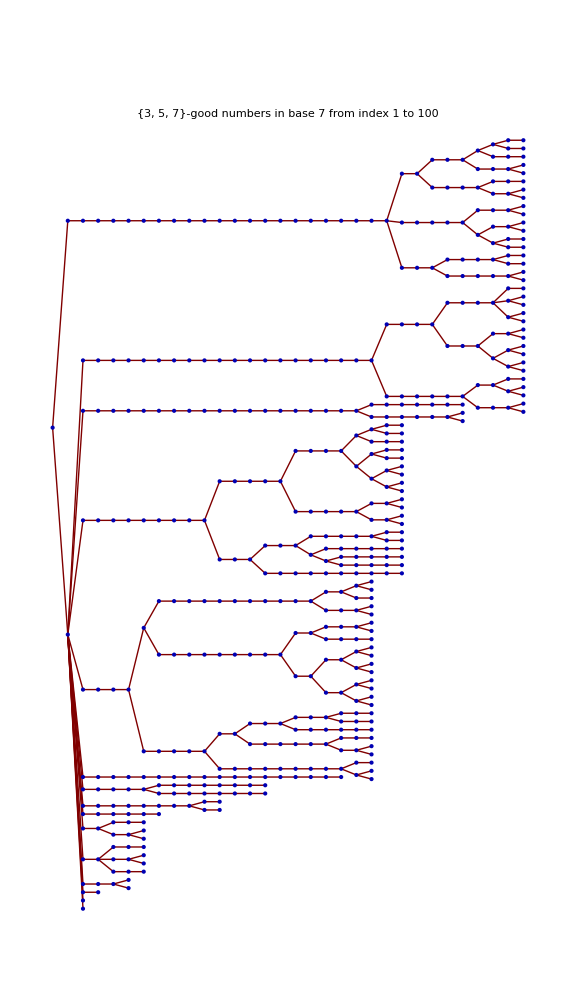

```mathematica
With[{tuple={3,5,7}, range={1,100}},
With[{g=GoodForTuple[tuple]},
Table[
TreePlot[
Flatten[Table[GraphForNumber2[n,p], {n,Take[g, {Max[1, range[[1]]], Min[Length[g], range[[2]]]}]}],1],
Left, 
MultiedgeStyle->None,
DirectedEdges->False,
VertexLabeling->False,
EdgeLabeling->False,
ImageSize->Large,
PlotLabel-> ToString[tuple] <> "-good numbers\nin base " <> ToString [p]  <>"\nfrom index " <> ToString[Max[1, range[[1]]] ]<> " to " <> ToString[ Min[Length[g], range[[2]]]],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger}
],
{p,tuple}
]
]
]
```